```mathematica
Vt=Vp*Exp[-t^2/(2 wV^2)]
```

ⅇ^(-t^2/(2 wV^2)) Vp

```mathematica
phi=PhiP*(Exp[-(x-x1)^2/(2 wphi^2)]-Exp[-(x-x2)^2/(2 wphi^2)])
```

(ⅇ^(-(x-x1)^2/(2 wphi^2))-ⅇ^(-(x-x2)^2/(2 wphi^2))) PhiP

```mathematica
sfap = InverseFourierTransform[-d^2*omega^2 Pi /(4*v^2)FourierTransform[Vt,t,omega,Assumptions->{wV>0}]*FourierTransform[phi,x,k,Assumptions->{wphi>0}]/.k->(omega/v),omega,t]
```

1/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+v^2 wV^2)^2)d^2 ⅇ^(-(-t v+x1)^2/(2 (wphi^2+v^2 wV^2))-(-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) PhiP π Vp √(v^2/(wphi^2+v^2 wV^2)) (-ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) t^2 v^2+ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) t^2 v^2+ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) wphi^2-ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) wphi^2+ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) v^2 wV^2-ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) v^2 wV^2-2 ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) t v x1+ⅇ^((-t v+x2)^2/(2 (wphi^2+v^2 wV^2))) x1^2+2 ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) t v x2-ⅇ^((-t v+x1)^2/(2 (wphi^2+v^2 wV^2))) x2^2) σ

```mathematica
sfap = sfap /.v->a*Sqrt[d]
```

1/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+a^2 d wV^2)^2)d^2 ⅇ^(-(-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))-(-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) PhiP π Vp √((a^2 d)/(wphi^2+a^2 d wV^2)) (-a^2 d ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) t^2+a^2 d ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) t^2+ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) wphi^2-ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) wphi^2+a^2 d ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) wV^2-a^2 d ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) wV^2-2 a √d ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) t x1+ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) x1^2+2 a √d ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) t x2-ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) x2^2) σ

```mathematica
sfap = sfap/.->1
```

1/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+a^2 d wV^2)^2)d^2 ⅇ^(-(-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))-(-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) PhiP π Vp √((a^2 d)/(wphi^2+a^2 d wV^2)) (-a^2 d ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) t^2+a^2 d ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) t^2+ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) wphi^2-ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) wphi^2+a^2 d ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) wV^2-a^2 d ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) wV^2-2 a √d ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) t x1+ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) x1^2+2 a √d ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) t x2-ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) x2^2)

```mathematica
Sfap[d_,t_,wphi_,PhiP_,x1_,x2_,Vp_,wV_,a_]:=1/(4 √(1/wphi^2) √(1/wV^2) (wphi^2+a^2 d wV^2)^2)d^2 ⅇ^(-(-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))-(-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) PhiP π Vp √((a^2 d)/(wphi^2+a^2 d wV^2)) (-a^2 d ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) t^2+a^2 d ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) t^2+ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) wphi^2-ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) wphi^2+a^2 d ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) wV^2-a^2 d ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) wV^2-2 a √d ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) t x1+ⅇ^((-a √d t+x2)^2/(2 (wphi^2+a^2 d wV^2))) x1^2+2 a √d ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) t x2-ⅇ^((-a √d t+x1)^2/(2 (wphi^2+a^2 d wV^2))) x2^2)
```

```mathematica
Wc[d_,a_,wPhi_,wV_]:=Sqrt[((wPhi/(a*Sqrt[d]))^2)+wV^2]
```

```mathematica
DExpected[d_,a_,wPhi_,wV_]:= (a*Sqrt[d])*Wc[d,a,wPhi,wV]
```

```mathematica
DExpected[0.0000001,465,.001,2*10^-4]
```

0.00100043

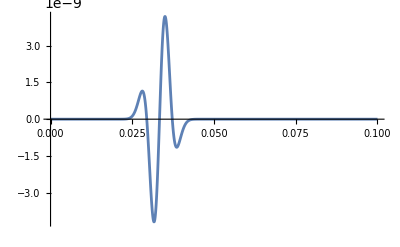

```mathematica
Plot[Sfap[0.000001,t,0.001,1000,0.015,0.016,.05, 2*10^-4,465],{t,0,0.1},PlotRange->All]
```

```mathematica
times = Subdivide[0,0.1,2000];
```

```mathematica
capValsSeparate = Table[Sfap[0.000001,t,0.001,1000,0.015,0.025,.05, 2*10^-4,465], {t,times}];
```

General::munfl: 4.91462×10^-8 2.20028×10^-301 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.91462×10^-8 6.60774×10^-302 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.91462×10^-8 1.98227×10^-302 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
capValsTogether = Table[Sfap[0.000001,t,0.001,1000,0.015,0.016,.05, 2*10^-4,465], {t,times}];
```

General::munfl: 4.91462×10^-8 1.48125×10^-301 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.91462×10^-8 4.3515×10^-302 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 4.91462×10^-8 1.27698×10^-302 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

```mathematica
Export["~/Documents/ReciprocityStuff/NANS/FENS/capUnmyelinSeparate.dat",capValsSeparate]
```

~/Documents/ReciprocityStuff/NANS/FENS/capUnmyelinSeparate.dat

```mathematica
Export["~/Documents/ReciprocityStuff/NANS/FENS/capUnmyelinTogether.dat",capValsTogether]
```

~/Documents/ReciprocityStuff/NANS/FENS/capUnmyelinTogether.dat